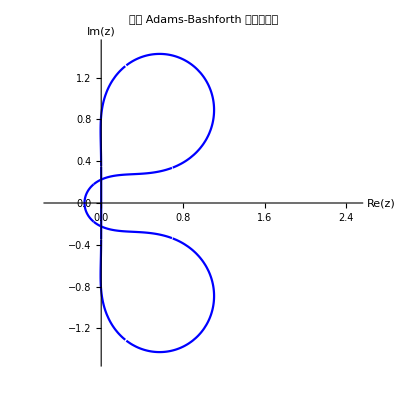

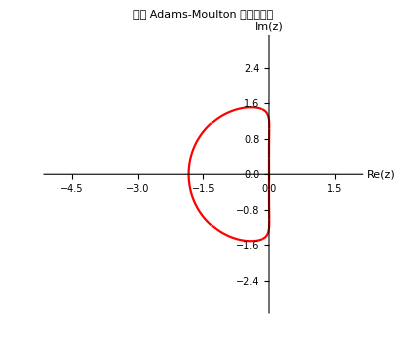

```mathematica
(*五阶 Adams-Bashforth*)rho[z_]:=z^5-z^4
sigmaAB[z_]:=(1901 z^4-2774 z^3+2616 z^2-1274 z+251)/720

boundaryAB=rho[E^(I t)]/sigmaAB[E^(I t)];

abPlot=ParametricPlot[{Re[boundaryAB],Im[boundaryAB]},{t,0,2 Pi},PlotRange->{{-0.5,2.5},{-1.5,1.5}},AspectRatio->Automatic,AxesLabel->{"Re(z)","Im(z)"},PlotLabel->"五阶 Adams-Bashforth 绝对稳定域",PlotStyle->Blue]

(*五阶 Adams-Moulton*)
sigmaAM[z_]:=(251 z^5+646 z^4-264 z^3+106 z^2-19 z)/720

boundaryAM=rho[E^(I t)]/sigmaAM[E^(I t)];

amPlot=ParametricPlot[{Re[boundaryAM],Im[boundaryAM]},{t,0,2 Pi},PlotRange->{{-5,2},{-3,3}},AspectRatio->Automatic,AxesLabel->{"Re(z)","Im(z)"},PlotLabel->"五阶 Adams-Moulton 绝对稳定域",PlotStyle->Red]
```

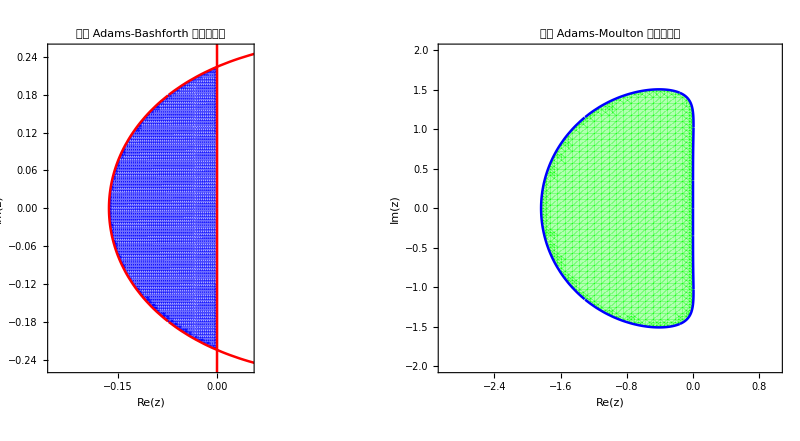

```mathematica
(* ============================================================五阶 Adams-Bashforth 与 五阶 Adams-Moulton 绝对稳定域 生成多项式：ρ(ζ)=ζ^5-ζ^4 稳定性条件：对测试方程 y'=λy，z=hλ，多项式 ρ(ζ)-z σ(ζ) 的所有根满足|ζ| ≤1============================================================*)(*公共 ρ 生成多项式*)rho[ζ_]:=ζ^5-ζ^4

(*-----五阶 Adams-Bashforth (显式)-----*)
sigmaAB[ζ_]:=(1901 ζ^4-2774 ζ^3+2616 ζ^2-1274 ζ+251)/720

(*-----五阶 Adams-Moulton (隐式)-----*)
sigmaAM[ζ_]:=(251 ζ^5+646 ζ^4-264 ζ^3+106 ζ^2-19 ζ)/720

(*-------------------------------------------------------------------稳定性判断函数：对给定的复数 z，计算 ρ(ζ)-z σ(ζ)=0 的所有根，如果所有根的模长都≤1（容许微小数值误差），则返回 True。-------------------------------------------------------------------*)
stableQ[z_,σ_]:=Module[{poly,roots},poly=rho[ζ]-z σ[ζ];
roots=ζ/.NSolve[poly==0,ζ];
Max[Abs[roots]]≤1+10^-6];

(*特化为两个方法的判别函数*)
stableQAB[z_]:=stableQ[z,sigmaAB]
stableQAM[z_]:=stableQ[z,sigmaAM]

(* ============================================================绘制五阶 Adams-Bashforth 绝对稳定域 区域非常小，需在原点附近放大并提高采样点============================================================*)
abRegion=RegionPlot[stableQAB[x+I y],{x,-0.25,0.05},{y,-0.25,0.25},PlotPoints->100,(*高采样点避免锯齿*)BoundaryStyle->None,PlotStyle->Directive[Blue,Opacity[0.35]],AspectRatio->Automatic];

abBoundary=ParametricPlot[{Re[rho[E^(I t)]/sigmaAB[E^(I t)]],Im[rho[E^(I t)]/sigmaAB[E^(I t)]]},{t,0,2 Pi},PlotStyle->Directive[Red,Thickness[0.005]]];

plotAB=Show[abRegion,abBoundary,PlotRange->{{-0.25,0.05},{-0.25,0.25}},Frame->True,FrameLabel->{"Re(z)","Im(z)"},PlotLabel->"五阶 Adams-Bashforth 绝对稳定域",ImageSize->Medium];

(* ============================================================绘制五阶 Adams-Moulton 绝对稳定域 区域较大，可直接用适中的采样点============================================================*)
amRegion=RegionPlot[stableQAM[x+I y],{x,-5,2},{y,-3,3},PlotPoints->80,BoundaryStyle->None,PlotStyle->Directive[Green,Opacity[0.3]],AspectRatio->Automatic];

amBoundary=ParametricPlot[{Re[rho[E^(I t)]/sigmaAM[E^(I t)]],Im[rho[E^(I t)]/sigmaAM[E^(I t)]]},{t,0,2 Pi},PlotStyle->Directive[Blue,Thickness[0.005]]];

plotAM=Show[amRegion,amBoundary,PlotRange->{{-3,1},{-2,2}},Frame->True,FrameLabel->{"Re(z)","Im(z)"},PlotLabel->"五阶 Adams-Moulton 绝对稳定域",ImageSize->Medium];

(*并排显示两个图形*)
GraphicsRow[{plotAB,plotAM},Spacings->Scaled[0.02]]
```

```mathematica
Export["D:\\word\\note\\数值分析\\hw\\hw11\\result.png",%66,"PNG"]
```

D:\word\note\数值分析\hw\hw11\result.png